```mathematica
?AxesOrigin
```

AxesOrigin is an option for graphics functions that specifies where any axes drawn should cross.

```mathematica
Manipulate[Labeled[Framed[Graphics[Circle[{0,0},3],PlotRange->3,ImagePadding->20,Axes->True,AxesOrigin->p]],p],{{p,{0,0}},Locator}]
```

```mathematica
?Rectangle
```

Rectangle[{x_min,y_min},{x_max,y_max}] represents an axis-aligned filled rectangle from {x_min,y_min} to {x_max,y_max}.
Rectangle[{x_min,y_min}] corresponds to a unit square with its bottom-left corner at {x_min,y_min}.

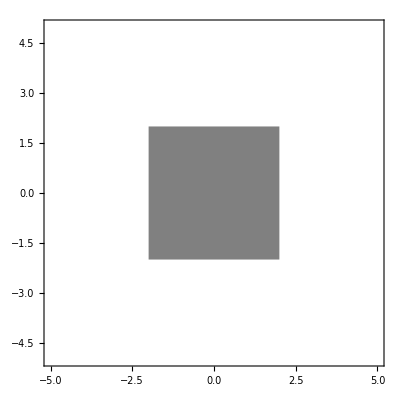

```mathematica
Graphics[{Gray,Rectangle[{xmin,ymin},{xmax,ymax}]},PlotRange->{{-5,5},{-5,5}},Frame->True]
```

```mathematica
?Locator
```

Locator[{x,y}] represents a locator object at position {x,y} in a graphic. 
Locator[Dynamic[pos]] takes the position to be the dynamically updated current value of pos, with this value being reset if the locator object is moved. 
Locator[{x,y},obj] displays obj as the locator object. 
Locator[{x,y},None] displays nothing visible as the locator object.

```mathematica
xmin=-2;
xmax=2;
ymin=-2;
ymax=2;
prmin=-5;
prmax=5;

f[x_,y_]:=-(x^2+y^2)/10
fx=D[f[x,y],x];
fy=D[f[x,y],y];
grad[x_,y_]=Grad[f[x,y],{x,y}];

DynamicModule[{
pt={0,0}
},{
LocatorPane[Dynamic[pt],Dynamic@Graphics[{Gray,Rectangle[{pt[[1]]+Max[xmin,prmin-pt[[1]]],pt[[2]]+Max[ymin,prmin-pt[[2]]]},{pt[[1]]+xmax,pt[[2]]+ymax}]},PlotRange->{{prmin,prmax},{prmin,prmax}},Frame->True]],
Dynamic[{Show[{
Plot3D[{
f[x,y],
(fx/.{x->pt[[1]],y->pt[[2]]})(x-pt[[1]])+(fy/.{x->pt[[1]],y->pt[[2]]})(y-pt[[2]])+f[pt[[1]],pt[[2]]]
},
{x,-5,5},{y,-5,5},ImageSize->Scaled[0.8],PlotRange->{-5,5},ColorFunction->{Automatic,"AvocadoColors"}],
Graphics3D[{
{Black,PointSize[0.02],point=Point[{pt[[1]],pt[[2]],f[pt[[1]],pt[[2]]]}]},
(*{Red,PointSize[0.02],point2=Point[{grad[pt[[1]],pt[[2]]][[1]],grad[pt[[1]],pt[[2]]][[2]],Norm[grad[pt[[1]],pt[[2]]]]}]},*)
{Black,Thickness[0.005],
Arrow[{
{pt[[1]],pt[[2]],f[pt[[1]],pt[[2]]]},
{fx/.{x->pt[[1]],y->pt[[2]]},fy/.{x->pt[[1]],y->pt[[2]]},1}
}]}
}]
}]}]
}
]

pt2={2,1,3};
```

```mathematica
f[x_,y_]:=-(x^2+y^2)/10
```

```mathematica
grad[x_,y_]:=Grad[f[x,y],{x,y}];
```

```mathematica
normal[x_,y_]=Simplify[grad[x,y]/(√(grad[x,y].grad[x,y]))];
```

```mathematica
Manipulate[Quiet[ContourPlot[f[x,y],{x,-2,2},{y,-2,2}, Epilog->Arrow[{pt2,pt2+normal@@pt2}],PerformanceGoal->"Quality",Contours->20,PlotRange->{{-2,2},{-2,2},{-30,30}},ImageSize->Medium]],{{pt2,{0.01,0.01}},Locator},FrameLabel->"Click a point to see its normal",SaveDefinitions->True]
```

```mathematica
Union[Flatten[grad[pt[[1]],pt[[2]]]],{3}]
```

{0,3}

```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.

{2,3}

```mathematica
pt={2,3}
Graphics3D[Arrow[{
{pt[[1]],pt[[2]],f[pt[[1]],pt[[2]]]},{grad[pt[[1]],pt[[2]]][[1]],grad[pt[[1]],pt[[2]]][[2]],Norm[grad[pt[[1]],pt[[2]]]]}}]]
```

{2,3}

-Graphics3D-

```mathematica
?Arrow
```

Arrow[{pt_1,pt_2}] is a graphics primitive that represents an arrow from pt_1 to pt_2.
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2. 
Arrow[curve,…] represents an arrow following the specified curve.

```mathematica
ColorData[]
ColorData["Gradients"]
```

{Gradients,Indexed,Named,Physical}

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
z-z0=fx[x,y](x-x0)+fy[x,y](y-y0)
```

SetDelayed::write: Tag Plus in z-z0 is Protected.

$Failed

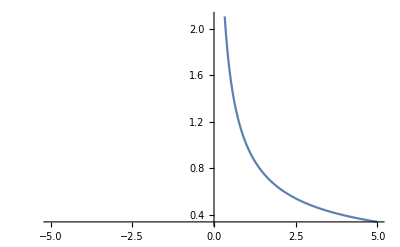

```mathematica
Plot[{x^(-2/3)},{x,-5,5}]
```

```mathematica
f[x_,y_]=Cos[x y]

{{D[f[x,y],x,x],D[f[x,y],x,y]},{D[f[x,y],y,x],D[f[x,y],y,y]}}

Det[%]
```

Cos[x y]

{{-y^2 Cos[x y],-x y Cos[x y]-Sin[x y]},{-x y Cos[x y]-Sin[x y],-x^2 Cos[x y]}}

-2 x y Cos[x y] Sin[x y]-Sin[x y]^2

```mathematica
DD[x_,y_]:=-2 x y Cos[x y] Sin[x y]-Sin[x y]^2
```

```mathematica
DD[0,0]Pl
```

0

```mathematica
Plot3D[f[x,y],{x,-5,5},{y,-5,5},ImageSize->Scaled[0.75]]
```

-Graphics3D-

```mathematica
pt={2,0,f[2,0]};
Show[{
Plot3D[{
f[x,y],
(fx/.{x->pt[[1]],y->pt[[2]]})(x-pt[[1]])+(fy/.{x->pt[[1]],y->pt[[2]]})(y-pt[[2]])+f[pt[[1]],pt[[2]]]
},
{x,-5,5},{y,-5,5}],
ParametricPlot3D[{pt[[1]]+(fx/.{x->pt[[1]],y->pt[[2]]}) t,pt[[2]]+(fy /.{x->pt[[1]],y->pt[[2]]})t, f[pt[[1]],pt[[2]]]-t},{t,-20,20},PlotStyle->Red]
},ImageSize->Scaled[0.9],PlotRange->{-5,5}]
```

-Graphics3D-

```mathematica
Show[{
Plot3D[
1-x-y,
{x,-5,5},{y,-5,5}],
ParametricPlot3D[{1+t,1+t,1+t},{t,-20,20},PlotStyle->Red]
},ImageSize->Scaled[0.9],PlotRange->{-5,5}]
```

-Graphics3D-